```mathematica
Off[SixJSymbol::tri];
Off[ThreeJSymbol::tri];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
$Assumptions=α∈Reals;
```

```mathematica
EMin=-100;
```

```mathematica
(* Save all the angular momentum coupling coefficients after computing once *)
JThree[{j1_,j1m_},{j2_,j2m_},{J_,Jm_}]:=JThree[{j1,j1m},{j2,j2m},{J,Jm}]=N[ThreeJSymbol[{j1,j1m},{j2,j2m},{J,Jm}]];
JSix[{j1_,j2_,j3_},{j4_,j5_,j6_}]:=JSix[{j1,j2,j3},{j4,j5,j6}]=N[SixJSymbol[{j1,j2,j3},{j4,j5,j6}]];
(* 9-j symbol ({{j1, j2, j12}, {j3, j4, j34}, {j13, j24, j}})*)
JNine[{j1_,j2_,j12_},{j3_,j4_,j34_},{j13_,j24_,j_}]:=JNine[{j1,j2,j12},{j3,j4,j34},{j13,j24,j}]=N[Sum[(-1)^(2g)(2g+1)JSix[{j1,j2,j12},{j34,j,g}]JSix[{j3,j4,j34},{j2,g,j24}]JSix[{j13,j24,j},{g,j1,j3}],{g,Max[Abs[j1-j],Abs[j2-j34],Abs[j3-j24]],Min[j1+j,j2+j34,j3+j24],1-Mod[2*(j1+j),2]/2}]]
```

```mathematica
(* This is the actual reduced matrix element of q *)
q[n1_,l1_,n_,l_]:= (I (-1)^(l1+1))/JThree[{l1,0},{1,0},{l,0}] √(n!n1!Gamma[n+l+3./2.]Gamma[n1+l1+3./2.])Sum[(-1)^(m+m1)/(m!m1!(n-m)!(n1-m1)!Gamma[m+l+3./2.]Gamma[m1+l1+3./2.])Which[l1==l+1,(l+1.)/Sqrt[(2l+1.)(2l+3.)] (2.m Gamma[m+m1+1.+(l+l1)/2.]-Gamma[m+m1+2.+(l+l1)/2.]),l1==l-1,l/Sqrt[(2.l+1.)(2.l-1.)]((2.m+2.l+1.) Gamma[m+m1+1.+(l+l1)/2.]-Gamma[m+m1+2.+(l+l1)/2.]),True,0],{m,0,n},{m1,0,n1}];
```

```mathematica
V[n1_,l1_,j1_,j1z_,n_,l_,j_,jz_]:=6.I (-1)^(j1-j1z)N[JThree[{j1,-j1z},{1,0},{j,jz}]Sqrt[(2j+1.)(2j1+1.)]JNine[{l1,l,1},{1/2,1/2,1},{j1,j,1}]q[n1,l1,n,l]]
```

```mathematica
(* Indexing of states *)
Nmax=10;
ni[1]=0;li[1]=j0-1/2;mi[1]=0;
imax=0;
i=0;
For[NShell=0,NShell≤Nmax,NShell++,
For[n=0,2n≤NShell,++n,
l=NShell-2n;
For[j=Abs[l-1/2],j≤Abs[l+1/2],j++,
For[jz=-j,jz≤j,jz++,
imax+=1;i+=1;
ni[i]=n;li[i]=l;ji[i]=j;jzi[i]=jz;
(*Print["N_shell=",2n+l,"   |",i,">=|",n,"(",l,s,")",j,jz,">"];*)
]]]]
Clear[i,l,m,n];
Print["There are a total of ",imax," ","included states."]
```

There are a total of 572 included states.

```mathematica
(*H0=Table[H[ni[i],li[i],ji[i],jzi[i],ni[j],li[j],ji[j],jzi[j]],{i,1,imax},{j,1,imax}];
(*H0//MatrixForm//FullSimplify*)
HermitianMatrixQ[ReplaceAll[H0,α->1]]*)
```

```mathematica
V0=Table[0,{i,1,imax},{j,1,imax}];
For[i=1,i≤imax,++i,
For[j=1,j<i,j++,V0[[i,j]]=If[jzi[i]==jzi[j]&&Abs[li[i]-li[j]]==1,V[ni[i],li[i],ji[i],jzi[i],ni[j],li[j],ji[j],jzi[j]],0]]]
V0=SparseArray[N[V0+Transpose[Conjugate[V0]]]];H0=SparseArray[N[DiagonalMatrix[Table[2ni[i]+li[i]+3/2-EMin,{i,1,imax}]]]];
```

```mathematica
(H0+αCalc[2]*V0)[[1;;5,1;;5]]//MatrixForm
```

(101.5+0. ⅈ | 0.+0. ⅈ | 0.0816497+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 101.5+0. ⅈ | 0.+0. ⅈ | -0.0816497+0. ⅈ | 0.+0. ⅈ
0.0816497+0. ⅈ | 0.+0. ⅈ | 102.5+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.0816497+0. ⅈ | 0.+0. ⅈ | 102.5+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 102.5+0. ⅈ)

```mathematica
(*Energies[α0_]:=Sort[Eigenvalues[N[ReplaceAll[H0,α->α0]]]]*)
α0Min=0;α0Max=2;α0Step=1/20;
αCalc[i_]:=N[α0Min+i*α0Step]
nEigValues=20;
Clear[Energies];
Timing[For[i=0,αCalc[i]≤α0Max,i++,
Energies[i]=Sort[Eigenvalues[H0+αCalc[i]*V0,-nEigValues]+EMin];]]
nSteps=i-1
For[j=1,j≤nEigValues,j++,Data[j]=Table[{αCalc[i],Evaluate[Energies[i]][[j]]},{i,0,nSteps}]]
```

{6.65524,Null}

40

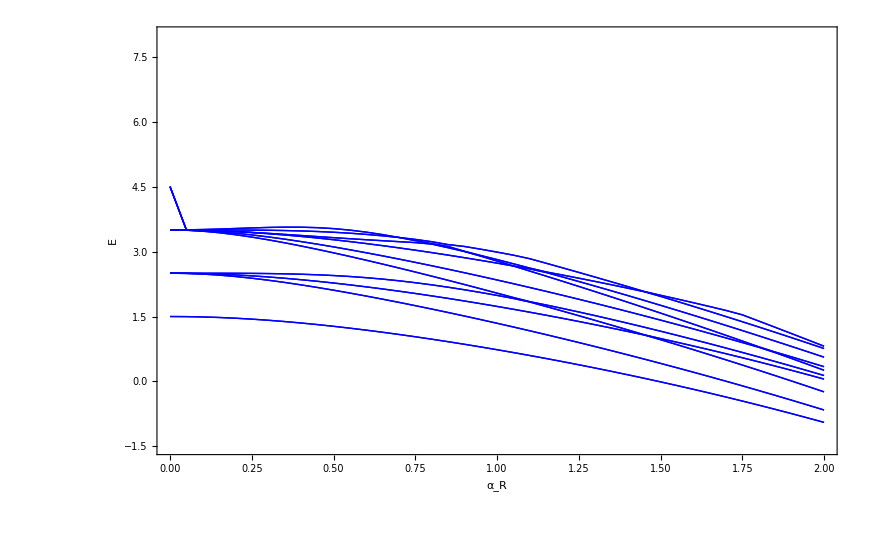

```mathematica
ListPlot[Table[Data[i],{i,1,nEigValues,1}],Joined->True,PlotRange->{{α0Min,α0Max},{-1.5,8}},Frame->True,FrameLabel->{"α_R","E"},PlotStyle->Directive[Blue]]
```

```mathematica
counter=0;
For[i=1,i≤nEigValues,i+=1,
For[j=i,j≤nEigValues,j+=1,
counter++;
Data2[counter]=Table[{αCalc[k],Energies[k][[i]]+Energies[k][[j]]},{k,0,nSteps}]]]
```

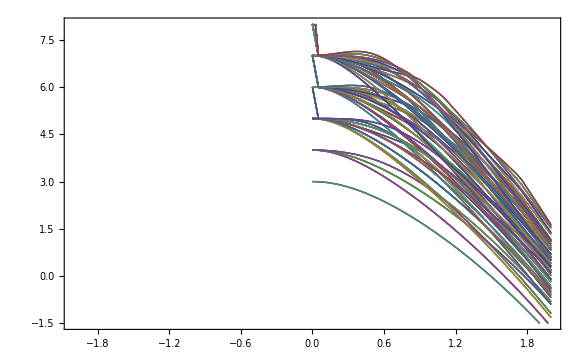

```mathematica
ListPlot[Table[Data2[x],{x,1,counter}],Joined->True,PlotRange->{{-2,2},{-1.5,8}},Frame->True]
```